```mathematica
f1 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.375)]+0.5,0.25≤x<0.75},{0,0≤x<0.25},{0,0.75≤x≤1}}]+RandomReal[{0,0.05}],{x,0,1, 1/100}]
f2 = Table[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.375},{0,0.875≤x≤1}}] +RandomReal[{0,0.05}], {x, 0,1,1/100}]
```

{0.0139262,0.0124571,0.00279749,0.0402656,0.0447598,0.0366038,0.036894,0.0451222,0.0461493,0.026569,0.0175424,0.0148699,0.00765162,0.0295893,0.0424663,0.0136686,0.00161421,0.0399542,0.0334274,0.0323585,0.0156848,0.0411077,0.00210587,0.0418186,0.00137438,0.0110897,0.053786,0.0425288,0.0486866,0.0801057,0.144978,0.183623,0.192704,0.258555,0.297503,0.352608,0.418131,0.498987,0.548596,0.605414,0.656247,0.728681,0.776213,0.842568,0.890914,0.919656,0.94915,0.983417,1.00334,1.02818,1.03586,1.01681,1.02691,1.00196,0.939587,0.916659,0.86766,0.852074,0.788209,0.717603,0.674387,0.606901,0.551519,0.486617,0.432728,0.379245,0.32735,0.232997,0.196106,0.176066,0.101617,0.0854788,0.0652284,0.0601902,0.0514903,0.00869664,0.00236534,0.0341325,0.0129786,0.0132774,0.0496911,0.0169114,0.0452795,0.0407367,0.00397246,0.0399696,0.00174411,0.0379593,0.0127916,0.00144889,0.0455235,0.0341726,0.0186504,0.0226548,0.0383756,0.0213228,0.00685865,0.0469557,0.00417164,0.00157669,0.00923329}

{0.0433452,0.00400816,0.0439653,0.0287477,0.0225262,0.0102955,0.00073925,0.0230607,0.0288516,0.0132526,0.0406098,0.0378141,0.0233754,0.0374207,0.0188184,0.0482935,0.00988439,0.00640444,0.0202984,0.0480628,0.0185853,0.0349704,0.0233234,0.0488481,0.0324006,0.00673032,0.0494588,0.00253157,0.0162344,0.0366367,0.0421362,0.0065688,0.0283541,0.00540815,0.00513127,0.00639564,0.00849602,0.0272576,0.00756365,0.0335246,0.0339077,0.0521731,0.116308,0.143867,0.173058,0.226783,0.281061,0.354102,0.409364,0.48636,0.523331,0.591792,0.635417,0.732238,0.752908,0.828642,0.877055,0.910857,0.964916,0.992799,0.986374,1.01277,1.02212,1.00813,0.992741,0.996879,0.968428,0.947079,0.902866,0.883481,0.827553,0.754571,0.725282,0.64904,0.597498,0.545034,0.459802,0.398959,0.334264,0.282457,0.251685,0.184903,0.155515,0.0806537,0.0856506,0.0478205,0.04452,0.00213474,0.0246472,0.0447784,0.00233488,0.0153593,0.00990343,0.0293259,0.0450678,0.0253329,0.0102723,0.0175195,0.0215184,0.0250128,0.0304004}

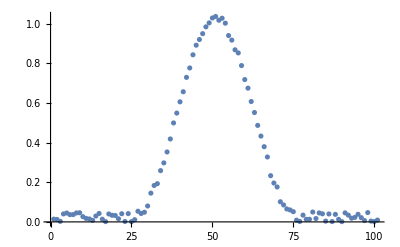

```mathematica
ListPlot[f1]
```

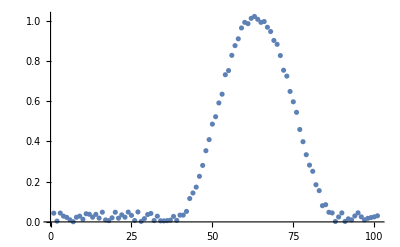

```mathematica
ListPlot[f2]
```

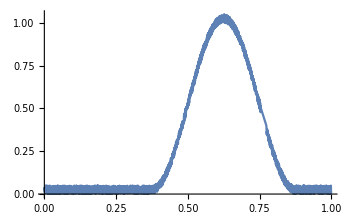

```mathematica
Plot[Piecewise[{{0.5*Sin[4*Pi*(x-0.5)]+0.5,0.375≤x<0.875},{0,0≤x<0.375},{0,0.875≤x≤1}}]+RandomReal[{0,0.05}],{x,0,1}]
```

```mathematica
Export[NotebookDirectory[]<>"plot1.svg",ListPlot[f1]]
Export[NotebookDirectory[]<>"plot2.svg", ListPlot[f2]]
```

/home/staff/scherping/CPP/projects/calibration/plot1.svg

/home/staff/scherping/CPP/projects/calibration/plot2.svg

```mathematica
Export[NotebookDirectory[]<>"plot1.csv", f1]
Export[NotebookDirectory[]<>"plot2.csv", f2]
```

/home/staff/scherping/CPP/projects/calibration/plot1.csv

/home/staff/scherping/CPP/projects/calibration/plot2.csv

ListPlot::lpn: RandomFunction[WhiteNoiseProcess[UniformDistribution[{0.,0.5}]],{0.,1.}] is not a list of numbers or pairs of numbers.

ListPlot::lpn: RandomFunction[WhiteNoiseProcess[ExponentialDistribution[5.]],{0.,1.}] is not a list of numbers or pairs of numbers.

RandomFunction::unsproc: The specification WhiteNoiseProcess[NormalDistribution[0,1]] is not a random process recognized by the system.

ListPlot::lpn: RandomFunction[WhiteNoiseProcess[NormalDistribution[0.,1.]],{0.,1.,40.}] is not a list of numbers or pairs of numbers.